```mathematica
(* Guy Mongelli                                ChE 400
Prof. Clark                                   10/25/2010    *)
```

```mathematica
(*Assignment #7 Challenge Problem   *)
```

```mathematica
a=1
```

1

```mathematica
(* This notebook assumes that the derivative of N is equal to zero at x=a, instead of z=a.  I aplogize for any confusion associated with this  *)
```

```mathematica
(*These are the eigenfunctions in the z-direction  *)
```

```mathematica
Clear[c]
```

```mathematica
F[z_,r_]:=Sin[((r-(1/2)) π z)/c]
```

```mathematica
(*Defining the derivative of the eigenfunctions in the z-direction *)
```

```mathematica
G[z_,r_]=D[F[z,r], z]
```

(π (-1/2+r) Cos[(π (-1/2+r) z)/c])/c

```mathematica
H[x_,r_]:=D[G[x,r], z]
```

```mathematica
F[z,1]
```

Sin[(π z)/(2 c)]

```mathematica
F[z,1]
```

Sin[(π z)/(2 c)]

```mathematica
H[z,r]
```

-(π^2 (-1/2+r)^2 Sin[(π (-1/2+r) z)/c])/c^2

```mathematica
H[z,r]
```

-(π^2 (-1/2+r)^2 Sin[(π (-1/2+r) z)/c])/c^2

```mathematica
Clear[a]
```

```mathematica
FullSimplify[F[z,r]/H[z,r],Element[{n,a},Integers]]
```

-(4 c^2)/(π^2 (1-2 r)^2)

```mathematica
(*These are the eigenvalues for the x-direction  *)
```

```mathematica
c=1
```

1

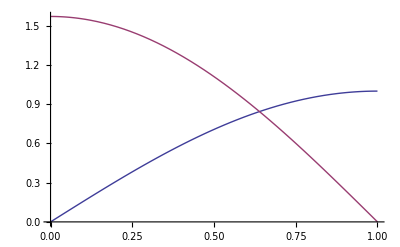

```mathematica
Plot[{F[z,1],G[z,1]},{z,0,c}]
```

```mathematica
N[F[0,1],2]
```

0

```mathematica
N[G[a,1],2]
```

1.6 Cos[1.6 a]

```mathematica
(*Defining the eigenfunctions in the x and y directions for comparison  *)
```

```mathematica
b=1;
c=1;
```

```mathematica
J[y_,q_]:=Sin[(q π y)/b]
```

```mathematica
K[x_,p_]:=Sin[(p π x)/c]
```

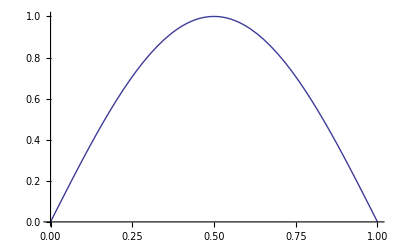

```mathematica
Plot[J[x,1],{x,0,c}]
```

```mathematica
Manipulate[Plot3D[F[x,1]J[y,1]K[z,1],{x,0,a},{y,0,b},PlotRange->{-1,1}],{z,0,c}]
```

Plot3D::plln: Limiting value a in {x, 0, a} is not a machine-size real number.

```mathematica
ClearAll
```

ClearAll

```mathematica
Clear[d]
```

```mathematica
(*The eigenvalues for the cubic reactor with the surface flux of one face equal to zero *)
```

```mathematica
Sigma1[p_,q_,r_]=D*((p^2 π^2)/d^2+(q^2 π^2)/d^2-((4 d^2)/(π^2 (1-2 r)^2))^-1-α+β)
```

D ((p^2 π^2)/d^2+(π^2 q^2)/d^2-(π^2 (1-2 r)^2)/(4 d^2)-α+β)

```mathematica
Sigma1[1,1,1]
```

D ((7 π^2)/(4 d^2)-α+β)

```mathematica
(* Solving for the eigenvalues of a cubic reactor with the neutron density equal to zero at all faces *)
```

```mathematica
Sigma2[p_,q_,r_]=D*((p^2 π^2)/d^2+(q^2 π^2)/d^2+(r^2 π^2)/d^2-α+β)
```

D ((p^2 π^2)/d^2+(π^2 q^2)/d^2+(π^2 r^2)/d^2-α+β)

```mathematica
Sigma2[1,1,1]
```

D ((3 π^2)/d^2-α+β)

```mathematica
Solve[Sigma1[1,1,1]==0,d]
```

{{d→-(√7 π)/(2 √(α-β))},{d→(√7 π)/(2 √(α-β))}}

```mathematica
Clear[d]
```

```mathematica
Solve[Sigma2[1,1,1]==0,d]
```

{{d→-(√3 π)/(√(α-β))},{d→(√3 π)/(√(α-β))}}

```mathematica
N[FullSimplify[(√7 π)/(2 √(α-β))/((√3 π)/(√(α-β))),Element[{α,β},Integers]],2]
```

0.76